# Compact Scheme Coefficients

## Hirschmann Research Group

## M Interior Scheme

### System

```mathematica
triRows[i_,j_,D_,k_]:=Module[{},
If[i-1==j, 1,
If[i==j, D,
If[i+1==j, 1,
0]
]
]
]
BoundTriMatrix[D_,k_]:=Array[triRows[#1,#2,D,k]&,{k,k}]

k=10; (*Size*)
MNormal=BoundTriMatrix[d,k];
MatrixForm[MNormal]
```

(d | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | d | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | d | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | d)

### First Derivative

#### Interior Rows

αϕ_(i+1)'+ϕ_i'+αϕ_(i-1)'=Σ_(k=1)a_k/(2kh)(ϕ_(i+k)-ϕ_(i-k))

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
(*NOTE: n must be EVEN*)
n=6;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
aList=Table[Symbol["a"<>ToString[i]],{i,1,n/2-1}];

(*If preserving the diagonal element, one less parameter (α) is needed*)
pars=Join[{α},aList];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n/2];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff}]==2*α+1;

(*Rest of the equations in the system*)
For[i=2,i<=n/2,i++,
system[[i]]=1/((2*i-1)!)*Sum[aList[[k]]*k^(2*i-2),{k,1,aLastCoeff}]==(2*α)/((2*i-2)!)
];

(*Print the list of coefficients found by solving the system*)
sols=Solve[system,pars][[1]]
N[sols,16]
```

{α,a1,a2}

{α→1/3,a1→14/9,a2→1/9}

{α→0.3333333333333333,a1→1.555555555555556,a2→0.1111111111111111}

### Second Derivative

#### Interior Rows

αϕ_(i+1)''+βϕ_i''+αϕ_(i-1)''=Σ_(k=1)a_k/(kh)^2(ϕ_(i+k)-2 ϕ_i+ϕ_(i-k))

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
(*NOTE: n must be EVEN*)
n=6;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
aList=Table[Symbol["a"<>ToString[i]],{i,1,n/2-1}];

(*If preserving the diagonal element, one less parameter (α) is needed*)
pars=Join[{α},aList];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n/2];
(*First equation in the system*)
system[[1]]=
1/(2!)*Sum[2aList[[k]](**(k-1)^0*),{k,1,aLastCoeff}]==2*α+β;

(*Rest of the equations in the system*)
For[i=2,i<=n/2,i++,
system[[i]]=1/((2*i)!)*Sum[2aList[[k]]*k^(2*i-2),{k,1,aLastCoeff}]==(2*α)/((2*i-2)!)
];

(*Print the list of coefficients found by solving the system*)
sols=Solve[system,pars][[1]]
N[sols,16]
```

{α,a1,a2}

{α→(2 β)/11,a1→(12 β)/11,a2→(3 β)/11}

{α→0.1818181818181818 β,a1→1.090909090909091 β,a2→0.2727272727272727 β}

## Boundary Schemes

## M̃ Scheme

### System

```mathematica
triRows[i_,j_,D_,k_]:=Module[{},
If[(i==1&&j==k),1,
If[(i==k&&j==1),1,
If[i-1==j, 1,
If[i==j, D,
If[i+1==j, 1,
0]
]
]
]
]
]
BoundTriMatrix[D_,k_]:=Array[triRows[#1,#2,D,k]&,{k,k}]

k=10; (*Size*)
MTilde=BoundTriMatrix[d,k];
MatrixForm[MTilde]
```

(d | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | d | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | d | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | d)

### First Derivative

#### Row 1

αϕ_i'+βϕ_(i+1)'+βϕ_N'=1/h[a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=6;
(*Preserve consistency of the diagonal element*)
keepDiag=True;
(*Size of the matrix*)
𝒩=100;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
If[keepDiag,
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-1}],
(*aList=Table[Subscript[a,i],{i,0,n-1}],*)
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-2}]
];

(*If preserving the diagonal element, one less parameter (α) is needed*)
If[keepDiag,
pars=Join[{β},aList],
pars=Join[{α,β},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff+1}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-1)^1,{k,1,aLastCoeff+1}]==α+2*β;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-1)^(i-1),{k,1,aLastCoeff+1}]==(β+𝒩^(i-2)*β)/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{α->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{β,a0,a1,a2,a3,a4,a5}

{β→5/2201387696,a0→-302696377597/132083261760,a1→133198509995/26416652352,a2→-11194333745/2201387696,a3→22580694995/6604163088,a4→-34163859995/26416652352,a5→9189750799/44027753920}

{β→2.27129460616373×10^-9,a0→-2.291708832471219,a1→5.042217621678152,a2→-5.085125970923025,a3→3.419160716371455,a4→-1.293269848872939,a5→0.2087263142175752}

### Second Derivative

#### Row 1

αϕ_i'+βϕ_(i+1)'+βϕ_N'=1/h[a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=6;
(*Preserve consistency of the diagonal element*)
keepDiag=True;
(*Size of the matrix*)
𝒩=100;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
If[keepDiag,
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-1}],
(*aList=Table[Subscript[a,i],{i,0,n-1}],*)
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-2}]
];

(*If preserving the diagonal element, one less parameter (α) is needed*)
If[keepDiag,
pars=Join[{β},aList],
pars=Join[{α,β},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff+1}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-1)^1,{k,1,aLastCoeff+1}]==α+2*β;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-1)^(i-1),{k,1,aLastCoeff+1}]==(β+𝒩^(i-2)*β)/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{α->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{β,a0,a1,a2,a3,a4,a5}

{β→5/2201387696,a0→-302696377597/132083261760,a1→133198509995/26416652352,a2→-11194333745/2201387696,a3→22580694995/6604163088,a4→-34163859995/26416652352,a5→9189750799/44027753920}

{β→2.27129460616373×10^-9,a0→-2.291708832471219,a1→5.042217621678152,a2→-5.085125970923025,a3→3.419160716371455,a4→-1.293269848872939,a5→0.2087263142175752}

## M̂ Scheme

### System

```mathematica
triRows[i_,j_,D_,k_]:=Module[{},
If[(i==1&&j==2)||(i==k&&j==k-1),β,
If[(i==1&&j==3)||(i==k&&j==k-2),γ,
If[i-1==j, 1,
If[i==j, D,
If[i+1==j, 1,
0]
]
]
]
]
]
BoundTriMatrix[D_,k_]:=Array[triRows[#1,#2,D,k]&,{k,k}]

k=10; (*Size*)
MHat=BoundTriMatrix[d,k];
MatrixForm[MHat]
```

(d | β | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | d | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | d | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | γ | β | d)

### First Derivative

#### Row 1

αϕ_i'+βϕ_(i+1)'+γϕ_(i+2)'=1/h[a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
If[keepDiag,
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-2}],
(*aList=Table[Subscript[a,i],{i,0,n-1}],*)
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-3}]
];

(*If preserving the diagonal element, one less parameter (α) is needed*)
If[keepDiag,
pars=Join[{β,γ},aList],
pars=Join[{α,β,γ},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=aList[[1]]==0;
system[[2]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff+1}]==0;
(*Second equation in the system*)
system[[3]]=1/(1!)*Sum[aList[[k]]*(k-1)^1,{k,1,aLastCoeff+1}]==α+β+γ;

(*Rest of the equations in the system*)
For[i=4,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-1)^(i-1),{k,1,aLastCoeff+1}]==(β+2^(i-2)*γ)/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{α->1},
sols=Solve[system,pars][[1]]
];
system
sols
N[sols,16]
```

{β,γ,a0,a1,a2}

{a0==0,a0+a1+a2==0,a1+2 a2==α+β+γ,1/6 (a1+8 a2)==1/2 (β+4 γ),1/24 (a1+16 a2)==1/6 (β+8 γ)}

{β→-44/13,γ→-17/13,a0→0,a1→48/13,a2→-48/13}

{β→-3.384615384615385,γ→-1.307692307692308,a0→0,a1→3.692307692307692,a2→-3.692307692307692}

### Second Derivative

#### Row 1

αϕ_i''+βϕ_(i+1)''+γϕ_(i+2)''=1/h^2[a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
If[keepDiag,
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-2}],
(*aList=Table[Subscript[a,i],{i,0,n-1}],*)
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-3}]
];

(*If preserving the diagonal element, one less parameter (α) is needed*)
If[keepDiag,
pars=Join[{β,γ},aList],
pars=Join[{α,β,γ},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=aList[[1]]==0;
system[[2]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff+1}]==0;
(*Second equation in the system*)
system[[3]]=1/(1!)*Sum[aList[[k]]*(k-1)^1,{k,1,aLastCoeff+1}]==α+β+γ;

(*Rest of the equations in the system*)
For[i=4,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-1)^(i-1),{k,1,aLastCoeff+1}]==(β+2^(i-2)*γ)/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{α->1},
sols=Solve[system,pars][[1]]
];
system
sols
N[sols,16]
```

{β,γ,a0,a1,a2}

{a0==0,a0+a1+a2==0,a1+2 a2==α+β+γ,1/6 (a1+8 a2)==1/2 (β+4 γ),1/24 (a1+16 a2)==1/6 (β+8 γ)}

{β→-44/13,γ→-17/13,a0→0,a1→48/13,a2→-48/13}

{β→-3.384615384615385,γ→-1.307692307692308,a0→0,a1→3.692307692307692,a2→-3.692307692307692}

## M̄ Scheme

### System

```mathematica
triRows[i_,j_,D_,k_]:=Module[{},
If[(i==1&&j==2)||(i==k&&j==k-1),α,
If[(i==2&&j==1)||(i==k-1&&j==k),β,
If[(i==2&&j==3)||(i==k-1&&j==k-2),β,
If[i-1==j, 1,
If[i==j, D,
If[i+1==j, 1,
0]
]
]
]
]
]
]
BoundTriMatrix[D_,k_]:=Array[triRows[#1,#2,D,k]&,{k,k}]

k=10; (*Size*)
MBar=BoundTriMatrix[d,k];
MatrixForm[MBar]
```

(d | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
β | d | β | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | β | d | β
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | d)

### First Derivative

#### Row 1

αϕ_i'+βϕ_(i+1)'=1/h[a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
If[keepDiag,
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-1}],
(*aList=Table[Subscript[a,i],{i,0,n-1}],*)
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-2}]
];

(*If preserving the diagonal element, one less parameter (α) is needed*)
If[keepDiag,
pars=Join[{β},aList],
pars=Join[{α,β},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff+1}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-1)^1,{k,1,aLastCoeff+1}]==α+β;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-1)^(i-1),{k,1,aLastCoeff+1}]==β/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{α->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{β→3,a0→-17/6,a1→3/2,a2→3/2,a3→-1/6}

{β→3.,a0→-2.833333333333333,a1→1.5,a2→1.5,a3→-0.1666666666666667}

#### Row 2

αϕ_(i-1)'+βϕ_i'+αϕ_(i+1)'=1/h[a_-1 ϕ_(i-1)+a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy, treating negative Subscript[a, n] coefficients*)
(*Ex: Subscript[a, -1]=an1, Subscript[a, -2]=an2, Subscript[a, -3]=an3, etc.*)
If[keepDiag,
aList=Table[
If[i>=0,
Symbol["a"<>ToString[i]],
Symbol["an"<>ToString[Abs[i]]]
],{i,-1,n-2}],
aList=Table[
If[i>=0,
Symbol["a"<>ToString[i]],
Symbol["an"<>ToString[Abs[i]]]
],{i,-1,n-3}]
];

(*If preserving the diagonal element, one less parameter (β) is needed*)
If[keepDiag,
pars=Join[{α},aList],
pars=Join[{α,β},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-2)^0*),{k,1,aLastCoeff+2}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-2)^1,{k,1,aLastCoeff+2}]==2*α+β;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
If[
Mod[i,2]==1, (*If i is odd, but since there's n+1 equations, it's basically if n is even*)
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-2)^(i-1),{k,1,aLastCoeff+2}]==0, (*Even equations in Taylor Series*)
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-2)^(i-1),{k,1,aLastCoeff+2}]==(2*α)/((i-2)!) (*Odd equations in Taylor Series*)
]
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{β->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{α,an1,a0,a1,a2}

{α→1/4,an1→-3/4,a0→0,a1→3/4,a2→0}

{α→0.25,an1→-0.75,a0→0,a1→0.75,a2→0}

### Second Derivative

#### Row 1

αϕ_i'+βϕ_(i+1)'=1/h[a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
If[keepDiag,
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-1}],
(*aList=Table[Subscript[a,i],{i,0,n-1}],*)
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-2}]
];

(*If preserving the diagonal element, one less parameter (α) is needed*)
If[keepDiag,
pars=Join[{β},aList],
pars=Join[{α,β},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff+1}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-1)^1,{k,1,aLastCoeff+1}]==α+β;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-1)^(i-1),{k,1,aLastCoeff+1}]==β/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{α->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{β→3,a0→-17/6,a1→3/2,a2→3/2,a3→-1/6}

{β→3.,a0→-2.833333333333333,a1→1.5,a2→1.5,a3→-0.1666666666666667}

#### Row 2

αϕ_(i-1)'+βϕ_i'+αϕ_(i+1)'=1/h[a_-1 ϕ_(i-1)+a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy, treating negative Subscript[a, n] coefficients*)
(*Ex: Subscript[a, -1]=an1, Subscript[a, -2]=an2, Subscript[a, -3]=an3, etc.*)
If[keepDiag,
aList=Table[
If[i>=0,
Symbol["a"<>ToString[i]],
Symbol["an"<>ToString[Abs[i]]]
],{i,-1,n-2}],
aList=Table[
If[i>=0,
Symbol["a"<>ToString[i]],
Symbol["an"<>ToString[Abs[i]]]
],{i,-1,n-3}]
];

(*If preserving the diagonal element, one less parameter (β) is needed*)
If[keepDiag,
pars=Join[{α},aList],
pars=Join[{α,β},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-2)^0*),{k,1,aLastCoeff+2}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-2)^1,{k,1,aLastCoeff+2}]==2*α+β;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
If[
Mod[i,2]==1, (*If i is odd, but since there's n+1 equations, it's basically if n is even*)
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-2)^(i-1),{k,1,aLastCoeff+2}]==0, (*Even equations in Taylor Series*)
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-2)^(i-1),{k,1,aLastCoeff+2}]==(2*α)/((i-2)!) (*Odd equations in Taylor Series*)
]
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{β->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{α,an1,a0,a1,a2}

{α→1/4,an1→-3/4,a0→0,a1→3/4,a2→0}

{α→0.25,an1→-0.75,a0→0,a1→0.75,a2→0}

## M^` Scheme

### System

```mathematica
triRows[i_,j_,D_,k_]:=Module[{},
If[(i==1&&j==2)||(i==k&&j==k-1),α,
If[(i==2&&j==1)||(i==k-1&&j==k),β,
If[(i==2&&j==3)||(i==k-1&&j==k-2),γ,
If[i-1==j, 1,
If[i==j, D,
If[i+1==j, 1,
0]
]
]
]
]
]
]
BoundTriMatrix[D_,k_]:=Array[triRows[#1,#2,D,k]&,{k,k}]

k=10; (*Size*)
MAccent=BoundTriMatrix[d,k];
MatrixForm[MAccent]
```

(d | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
β | d | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | d | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | γ | d | β
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | d)

### First Derivative

#### Row 1

αϕ_i'+βϕ_(i+1)'=1/h[a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
If[keepDiag,
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-1}],
(*aList=Table[Subscript[a,i],{i,0,n-1}],*)
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-2}]
];

(*If preserving the diagonal element, one less parameter (α) is needed*)
If[keepDiag,
pars=Join[{β},aList],
pars=Join[{α,β},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff+1}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-1)^1,{k,1,aLastCoeff+1}]==α+β;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-1)^(i-1),{k,1,aLastCoeff+1}]==β/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{α->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{β,a0,a1,a2,a3}

{β→3,a0→-17/6,a1→3/2,a2→3/2,a3→-1/6}

{β→3.,a0→-2.833333333333333,a1→1.5,a2→1.5,a3→-0.1666666666666667}

#### Row 2

αϕ_(i-1)'+βϕ_i'+γϕ_(i+1)'=1/h[a_-1 ϕ_(i-1)+a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy, treating negative Subscript[a, n] coefficients*)
(*Ex: Subscript[a, -1]=an1, Subscript[a, -2]=an2, Subscript[a, -3]=an3, etc.*)
If[keepDiag,
aList=Table[
If[i>=0,
Symbol["a"<>ToString[i]],
Symbol["an"<>ToString[Abs[i]]]
],{i,-1,n-3}],
aList=Table[
If[i>=0,
Symbol["a"<>ToString[i]],
Symbol["an"<>ToString[Abs[i]]]
],{i,-1,n-4}]
];

(*If preserving the diagonal element, one less parameter (β) is needed*)
If[keepDiag,
pars=Join[{α,γ},aList],
pars=Join[{α,β,γ},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-2)^0*),{k,1,aLastCoeff+2}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-2)^1,{k,1,aLastCoeff+2}]==α+β+γ;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-2)^(i-1),{k,1,aLastCoeff+2}]==((-1)^i*α+γ)/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{β->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{α,γ,an1,a0,a1}

{α→1/4,γ→1/4,an1→-3/4,a0→0,a1→3/4}

{α→0.25,γ→0.25,an1→-0.75,a0→0,a1→0.75}

### Second Derivative

#### Row 1

αϕ_i'+βϕ_(i+1)'=1/h[a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy*)
If[keepDiag,
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-1}],
(*aList=Table[Subscript[a,i],{i,0,n-1}],*)
aList=Table[Symbol["a"<>ToString[i]],{i,0,n-2}]
];

(*If preserving the diagonal element, one less parameter (α) is needed*)
If[keepDiag,
pars=Join[{β},aList],
pars=Join[{α,β},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-1)^0*),{k,1,aLastCoeff+1}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-1)^1,{k,1,aLastCoeff+1}]==α+β;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-1)^(i-1),{k,1,aLastCoeff+1}]==β/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{α->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{β,a0,a1,a2,a3}

{β→3,a0→-17/6,a1→3/2,a2→3/2,a3→-1/6}

{β→3.,a0→-2.833333333333333,a1→1.5,a2→1.5,a3→-0.1666666666666667}

#### Row 2

αϕ_(i-1)'+βϕ_i'+γϕ_(i+1)'=1/h[a_-1 ϕ_(i-1)+a_0 ϕ_i+a_1 ϕ_(i+1)+a_2 ϕ_(i+2)+...]

```mathematica
Clear["`*"]

(*Choose desired order of accuracy O(h^n)*)
n=4;
(*Preserve consistency of the diagonal element*)
keepDiag=True;

(*Create a list of as many coefficients Subscript[a, n] that are needed for O(h^n) accuracy, treating negative Subscript[a, n] coefficients*)
(*Ex: Subscript[a, -1]=an1, Subscript[a, -2]=an2, Subscript[a, -3]=an3, etc.*)
If[keepDiag,
aList=Table[
If[i>=0,
Symbol["a"<>ToString[i]],
Symbol["an"<>ToString[Abs[i]]]
],{i,-1,n-3}],
aList=Table[
If[i>=0,
Symbol["a"<>ToString[i]],
Symbol["an"<>ToString[Abs[i]]]
],{i,-1,n-4}]
];

(*If preserving the diagonal element, one less parameter (β) is needed*)
If[keepDiag,
pars=Join[{α,γ},aList],
pars=Join[{α,β,γ},aList]
];

(*Find the index of the largest coefficient Subscript[a, n]*)
aLastCoeff=ToExpression[StringDelete[ToString[Last[aList]],"a"]];
pars



(*Initialize a blank system of n+1 equations*)
system=ConstantArray[Null,n+1];
(*First equation in the system*)
system[[1]]=
1/(0!)*Sum[aList[[k]](**(k-2)^0*),{k,1,aLastCoeff+2}]==0;
(*Second equation in the system*)
system[[2]]=1/(1!)*Sum[aList[[k]]*(k-2)^1,{k,1,aLastCoeff+2}]==α+β+γ;

(*Rest of the equations in the system*)
For[i=3,i<=n+1,i++,
system[[i]]=1/((i-1)!)*Sum[aList[[k]]*(k-2)^(i-1),{k,1,aLastCoeff+2}]==((-1)^i*α+γ)/((i-2)!)
];

(*Print the list of coefficients found by solving the system*)
If[keepDiag,
sols=Solve[system,pars][[1]]/.{β->1},
sols=Solve[system,pars][[1]]
];
sols
N[sols,16]
```

{α,γ,an1,a0,a1}

{α→1/4,γ→1/4,an1→-3/4,a0→0,a1→3/4}

{α→0.25,γ→0.25,an1→-0.75,a0→0,a1→0.75}

## Convergence Testing

## Define Matrices

```mathematica
lhsRows[i_,j_,D_,k_]:=Module[{},
If[(i==1&&j==2)||(i==k&&j==k-1),β01,
If[(i==2&&j==1)||(i==k-1&&j==k),α10,
If[(i==2&&j==3)||(i==k-1&&j==k-2),γ12,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
0
]]]]]]]
LHS[D_,k_]:=Array[lhsRows[#1,#2,D,k]&,{k,k}]

k=8; (*Size*)
MatrixForm[LHS[d,k]]
```

(1 | β01 | 0 | 0 | 0 | 0 | 0 | 0
α10 | 1 | γ12 | 0 | 0 | 0 | 0 | 0
0 | α | 1 | α | 0 | 0 | 0 | 0
0 | 0 | α | 1 | α | 0 | 0 | 0
0 | 0 | 0 | α | 1 | α | 0 | 0
0 | 0 | 0 | 0 | α | 1 | α | 0
0 | 0 | 0 | 0 | 0 | γ12 | 1 | α10
0 | 0 | 0 | 0 | 0 | 0 | β01 | 1)

```mathematica
rhsRows[i_,j_,D_,k_]:=Module[{},
If[(i==1&&j==1),a00,
If[(i==1&&j==2),a01,
If[(i==1&&j==3),a02,
If[(i==1&&j==4),a03,
If[(i==2&&j==1),a10,
If[(i==2&&j==2),a11,
If[(i==2&&j==3),a12,
(*If[(i==2&&j==4),a13,
If[(i==2&&j==5),a14,*)

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
(*If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,*)

If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
0
]]]]]]]]]]]]]]]]]](*]]]]*)
RHS[D_,k_]:=Array[rhsRows[#1,#2,D,k]&,{k,k}]

k=8; (*Size*)
MatrixForm[RHS[d,k]]
```

(a00 | a01 | a02 | a03 | 0 | 0 | 0 | 0
a10 | a11 | a12 | 0 | 0 | 0 | 0 | 0
0 | -a1 | 0 | a1 | 0 | 0 | 0 | 0
0 | 0 | -a1 | 0 | a1 | 0 | 0 | 0
0 | 0 | 0 | -a1 | 0 | a1 | 0 | 0
0 | 0 | 0 | 0 | -a1 | 0 | a1 | 0
0 | 0 | 0 | 0 | 0 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | -a03 | -a02 | -a01 | -a00)

## Perform Calculations

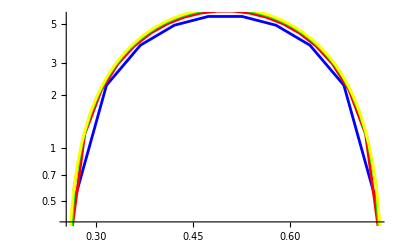

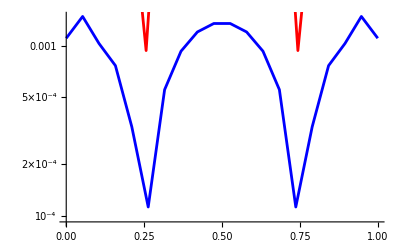

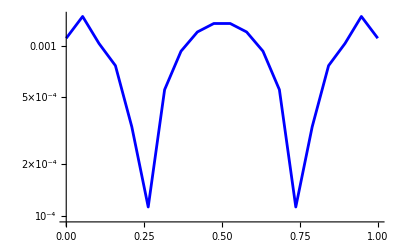
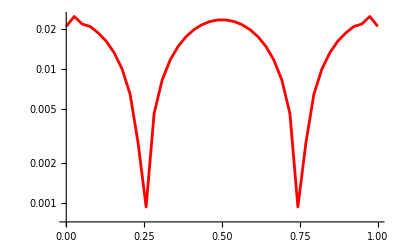
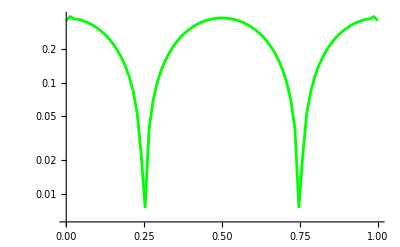
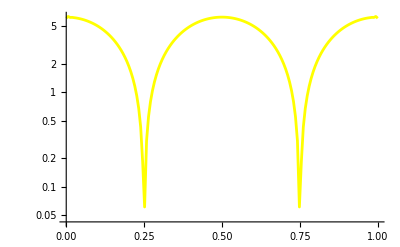

```mathematica
(*Define number of points and spacing*)
nList={20,40,80,160};
(*nList={20};*)
o=4;
xMax=1;
xMin=0;

(*Define coefficients*)
LHSRule={α->1/4,β01->3,α10->1/8,γ12->3/4};
RHSRule={a1->3/2,a00->-17/6,a01->3/2,a02->3/2,a03->-1/6,a10->-43/96,a11->-5/6,a12->9/8,a13->1/6,a14->-1/96};
LHSRule={α->1/4,β01->3,α10->1/4,γ12->1/4};
RHSRule={a1->3/2,a00->-17/6,a01->3/2,a02->3/2,a03->-1/6,a10->-3/4,a11->0,a12->3/4};

(*Define stuff for the loop*)
errorPlots=ConstantArray[Null,Length[nList]];
convergencePlots=ConstantArray[Null,Length[nList]];
colorList={Blue,Red,Green,Yellow};

(*Start loop*)
For[i=1,i<=Length[nList],i++,
n=nList[[i]];
h=(xMax-xMin)/(n-1);

(*Define analytical solution to d/dx[sin(2πx)]*)
x=Table[i,{i,xMin,xMax,h}];
ψ=Sin[2*π*x];
ψp=2*π*Cos[2*π*x];

(*Define numerical solution to d/dx[sin(2πx)]*)
A=LHS[d,n]/.LHSRule;
B=RHS[d,n]/.RHSRule;
AInv=Inverse[A];
(*AInv=MAcuteInv[1/(1/4),1/8,3,3/4,n];*)
CMat=AInv.B;
ϕ=Sin[2*π*x];
ϕp=CMat.ϕ;

(*Compute the error*)
error=ϕp-ψp;

(*Compute the convergence*)
If[n==160,normFactor=1,
If[n==80,normFactor=o^2,
If[n==40,normFactor=o^4,
If[n==20,normFactor=o^6
]]]];
normError=Abs[error]/normFactor;

(*Plot the error*)
errorList=Transpose[{x,error}];
errorPlots[[i]]=ListLogPlot[errorList,Joined->True,PlotStyle->colorList[[i]]];

(*Plot the convergence*)
normErrorList=Transpose[{x,normError}];
convergencePlots[[i]]=ListLogPlot[normErrorList,Joined->True,PlotStyle->colorList[[i]](*,PlotRange->{-2,2}*)];
]
A//MatrixForm;
AInv//MatrixForm//N;
B//MatrixForm;
CMat//MatrixForm//N;
error//N;

Show[errorPlots]
Show[convergencePlots]
convergencePlots
```